# GHZ STATES - Qiskit

## N = 2 DISCUSS THEORY-SIMULATION-RUN

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=2;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

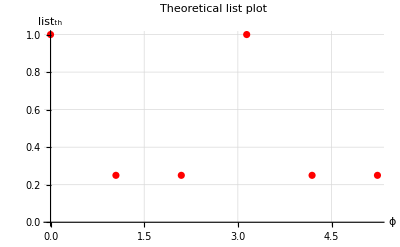

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

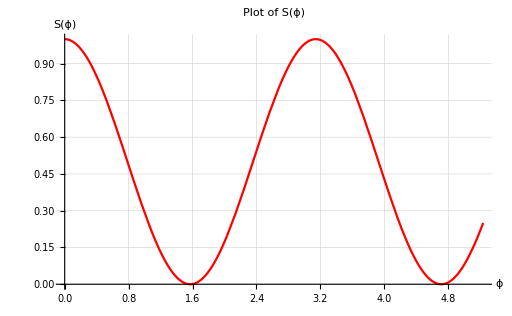

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

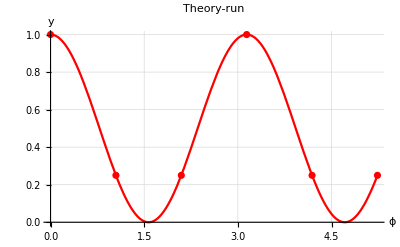

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

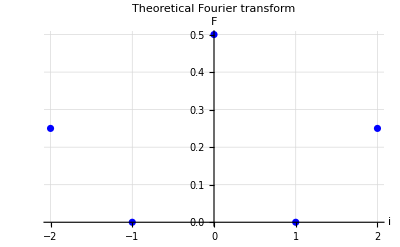

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

#### Data with the measurement of all qubit

```mathematica
data1={1.0,0.2431640625,0.2666015625,1.0,0.251953125,0.2451171875};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.243164,0.266602,1.,0.251953,0.245117}

6

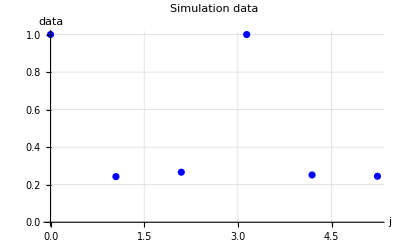

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

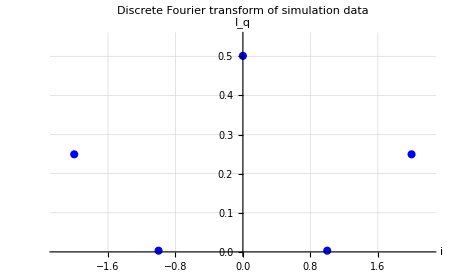

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

#### Data with the measurement of all qubit (000)

1024 SHOT:

```mathematica
data1={0.90625,0.33203125,0.2734375,0.9150390625,0.3359375,0.22265625}; (*Run on ibmqx2, 27 luglio 2019, ore 9:18*)
```

```mathematica
data2={0.9130859375,0.2978515625,0.255859375,0.919921875,0.3203125,0.28515625}; (*TRANSPILE Run on ibmqx2, 29 luglio 2019, ore 17:48, JOB ID:5d3f1355a99e6e0072a287d2 *)
```

```mathematica
data3={0.9189453125,0.3388671875,0.2763671875,0.916015625,0.31640625,0.240234375}; (*Transpile_user Run on ibmqx2, 29 luglio 2019, 17:55*)
```

```mathematica
data4={0.9072265625,0.302734375,0.24609375,0.9169921875,0.2880859375,0.248046875}; (*No Transpile Run on ibmqx2, 29 luglio 2019, 17:55*)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.913086,0.297852,0.255859,0.919922,0.320313,0.285156}

6

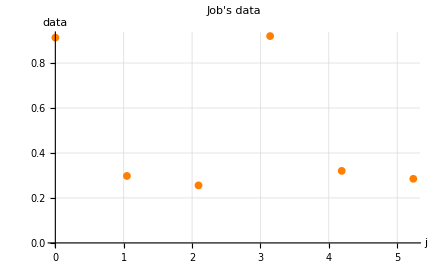

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

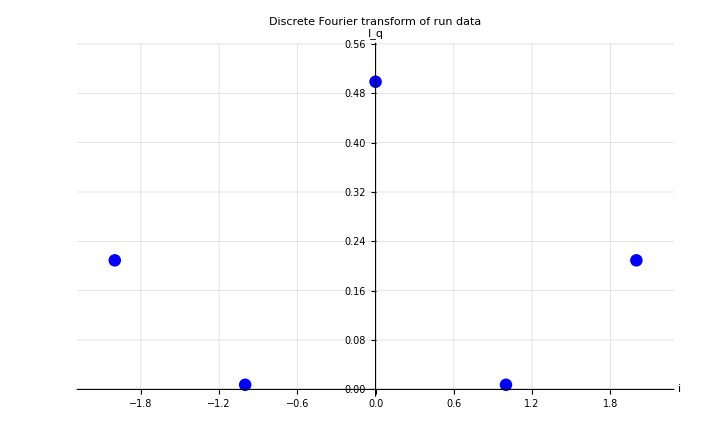

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

COMPARE

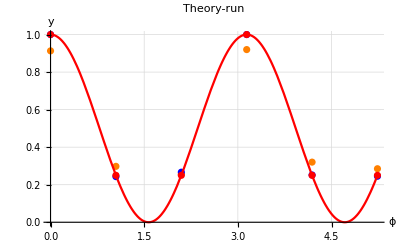

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

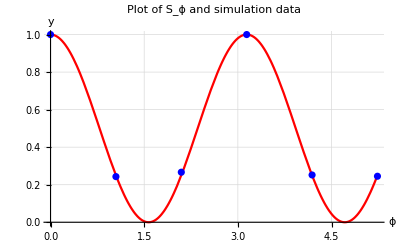

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

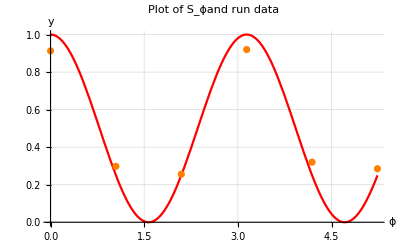

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

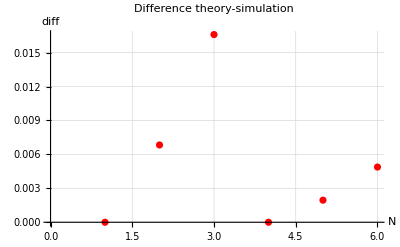

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

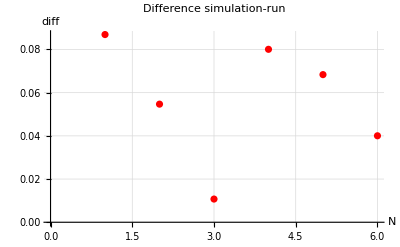

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

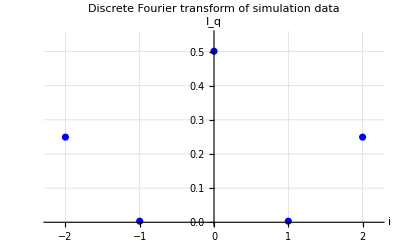

-Graphics-

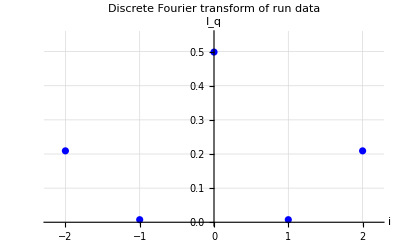

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 6 DISCUSS THEORY-SIMULATION-RUN

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=6;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

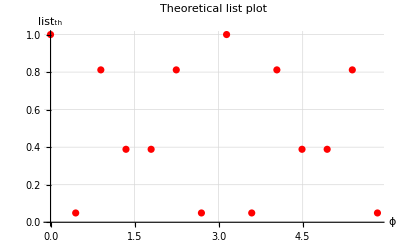

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

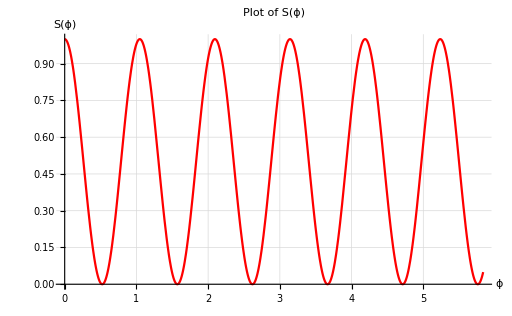

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

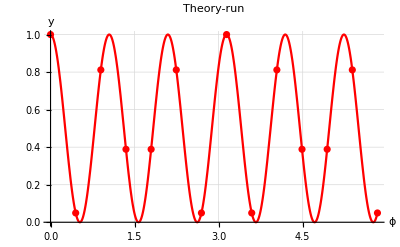

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-6,6}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-6,6}]]];
```

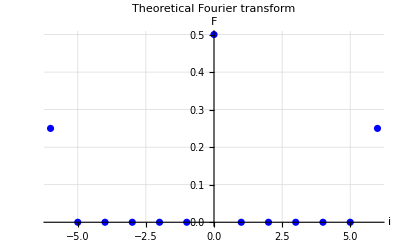

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

#### Data with the measurement of only qubit 0

```mathematica
data1={1.0,0.048828125,0.830078125,0.39453125,0.4013671875,0.8134765625,0.04296875,1.0,0.0498046875,0.8193359375,0.39453125,0.36328125,0.818359375,0.05078125}; 
data2={1.0,0.0546875,0.8095703125,0.3896484375,0.404296875,0.80859375,0.0458984375,1.0,0.0576171875,0.7900390625,0.3984375,0.4013671875,0.8154296875,0.052734375}; 
data3 = {1.0,0.04296875,0.8056640625,0.400390625,0.3798828125,0.80859375,0.0498046875,1.0,0.0556640625,0.8173828125,0.39453125,0.396484375,0.8203125,0.0517578125};
```

#### Data with the measurement of all qubit

```mathematica
data4={1.0,0.0458984375,0.7890625,0.3935546875,0.3994140625,0.8271484375,0.0498046875,1.0,0.052734375,0.8330078125,0.416015625,0.3837890625,0.8056640625,0.048828125};
```

```mathematica
data5={1.0,0.0537109375,0.8369140625,0.3955078125,0.3720703125,0.8330078125,0.0537109375,1.0,0.0400390625,0.8330078125,0.3818359375,0.40625,0.8271484375,0.0439453125};
```

```mathematica
data6={1.0,0.052734375,0.7939453125,0.3623046875,0.3876953125,0.818359375,0.048828125,1.0,0.04296875,0.8056640625,0.3779296875,0.4072265625,0.8154296875,0.0517578125};
```

#### Plot of the data choosen

```mathematica
simulation= data6
Length[simulation]
```

{1.,0.0527344,0.793945,0.362305,0.387695,0.818359,0.0488281,1.,0.0429688,0.805664,0.37793,0.407227,0.81543,0.0517578}

14

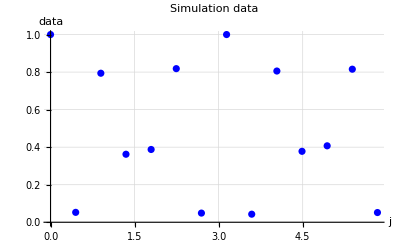

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-6,6}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-6,6}];
```

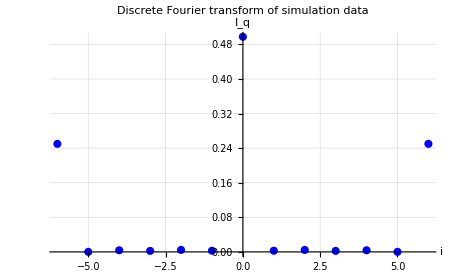

```mathematica
Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

#### Data with the measurement of only qubit 0

```mathematica
data1={0.5703125,0.58203125,0.5908203125,0.576171875,0.5712890625,0.564453125,0.5595703125,0.5517578125,0.5498046875,0.57421875,0.55078125,0.5322265625,0.5205078125,0.5576171875}; (*Run on ibmq_16_melbourne, solo qubit 0, 25 luglio 2019, ore 16:10*)
data2={0.53515625,0.5810546875,0.546875,0.5908203125,0.55078125,0.5400390625,0.5517578125,0.5322265625,0.583984375,0.5341796875,0.5595703125,0.5439453125,0.544921875,0.5224609375}; (*Run on ibmq_16_melbourne, solo qubit 0, 25 luglio 2019, ore 16:55*)
```

#### Data with the measurement of all qubit (000000)

```mathematica
data3={0.064453125,0.0615234375,0.056640625,0.0625,0.0517578125,0.072265625,0.0693359375,0.078125,0.056640625,0.0576171875,0.0576171875,0.0478515625,0.0576171875,0.0498046875}; (*Run on ibmq_16_melbourne, 25 luglio 2019, ore 17:36*)
```

```mathematica
data4={0.0703125,0.052734375,0.064453125,0.064453125,0.0546875,0.0654296875,0.0791015625,0.0615234375,0.0654296875,0.060546875,0.05078125,0.0517578125,0.0537109375,0.0478515625}; (*Run on ibmq_16_melbourne, 25 luglio 2019, ore 18:28*)
```

#### Plot of the data choosen

```mathematica
run=data4  (*inserire il data che si vuole*)
Length[run]
```

{0.0703125,0.0527344,0.0644531,0.0644531,0.0546875,0.0654297,0.0791016,0.0615234,0.0654297,0.0605469,0.0507813,0.0517578,0.0537109,0.0478516}

14

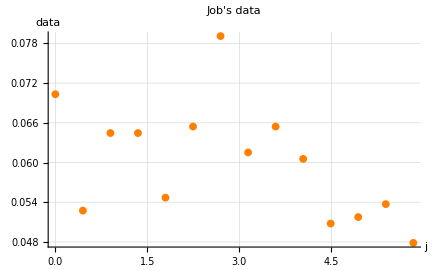

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-6,6}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-6,6}];
```

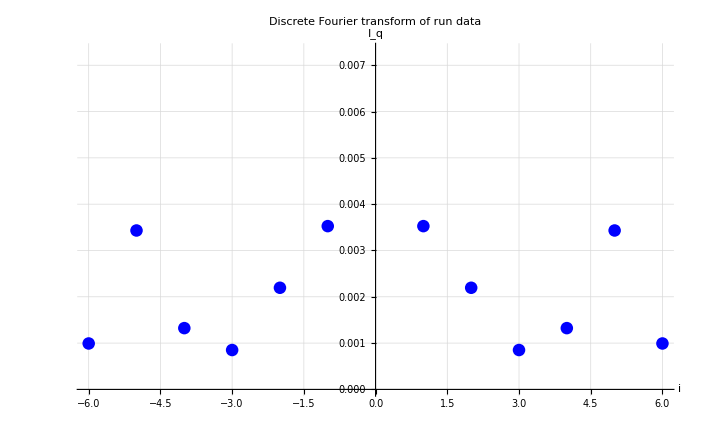

```mathematica
Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

COMPARE

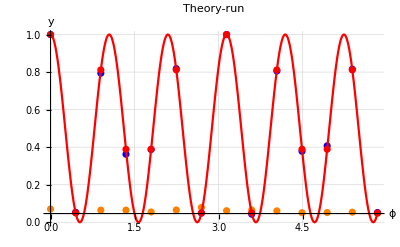

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

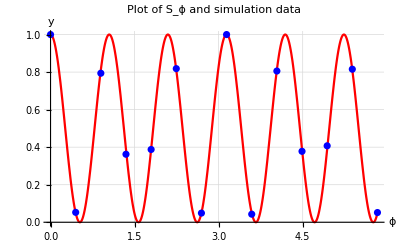

```mathematica
Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

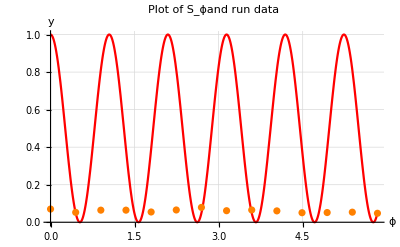

```mathematica
Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

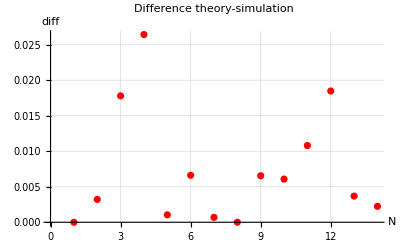

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

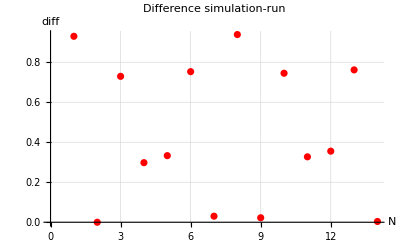

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

## N = 8 DISCUSS THEORY-SIMULATION-RUN

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=8;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

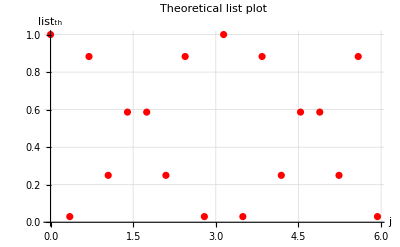

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["j"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

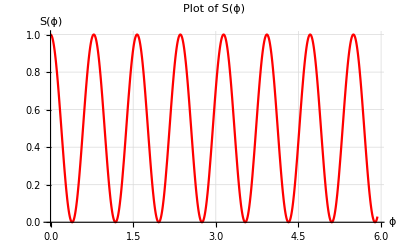

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

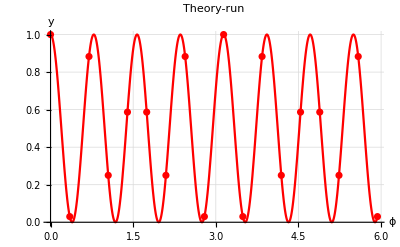

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-8,8}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-8,8}]]];
```

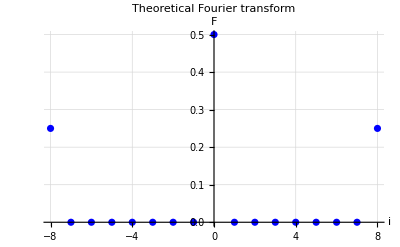

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

#### Data with the measurement of only qubit 0

```mathematica
data1={1.0,0.0302734375,0.88671875,0.2421875,0.59375,0.5986328125,0.2470703125,0.876953125,0.0302734375,1.0,0.029296875,0.8798828125,0.2578125,0.5751953125,0.5927734375,0.2421875,0.91015625,0.029296875};
data2={};
```

#### Data with the measurement of all qubit

```mathematica
data3={};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0302734,0.886719,0.242188,0.59375,0.598633,0.24707,0.876953,0.0302734,1.,0.0292969,0.879883,0.257813,0.575195,0.592773,0.242188,0.910156,0.0292969}

18

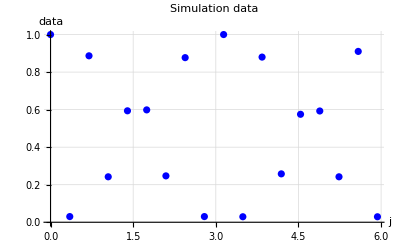

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-8,8}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-8,8}];
```

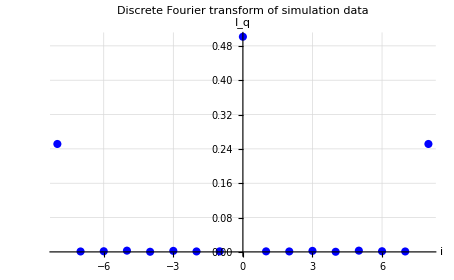

```mathematica
Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

#### Data with the measurement of only qubit 0

```mathematica
data1={0.515625,0.5244140625,0.5302734375,0.54296875,0.52734375,0.541015625,0.5302734375,0.5380859375,0.5625,0.51953125,0.52734375,0.5322265625,0.5517578125,0.5029296875,0.5244140625,0.53125,0.5341796875,0.544921875}; (*Run on ibmq_16_melbourne, solo qubit 0, 25 luglio 2019, ore 16:40*)
```

#### Data with the measurement of all qubit

```mathematica
data2={0.009765625,0.015625,0.0087890625,0.013671875,0.009765625,0.0107421875,0.009765625,0.0068359375,0.005859375,0.0087890625,0.00390625,0.0087890625,0.0087890625,0.0087890625,0.0146484375,0.017578125,0.0146484375,0.0087890625}; (*Run on ibmq_16_melbourne, 25 luglio 2019, ore ??? *)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.00976563,0.015625,0.00878906,0.0136719,0.00976563,0.0107422,0.00976563,0.00683594,0.00585938,0.00878906,0.00390625,0.00878906,0.00878906,0.00878906,0.0146484,0.0175781,0.0146484,0.00878906}

18

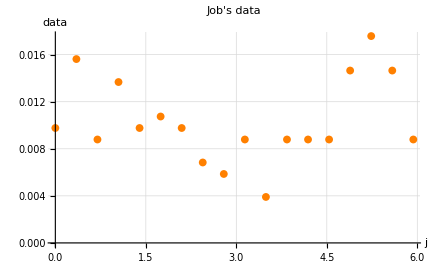

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-8,8}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-8,8}];
```

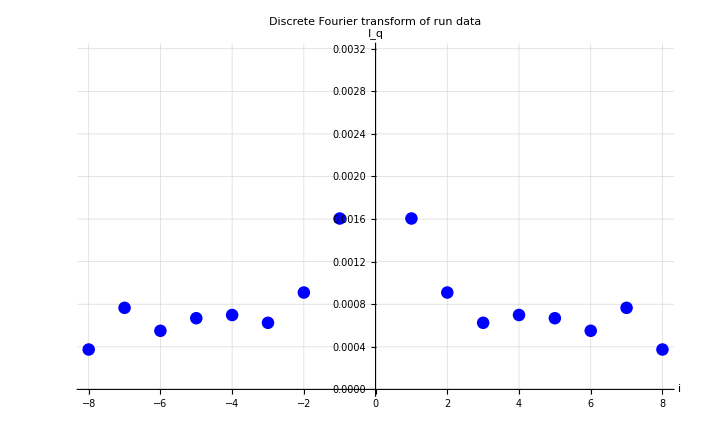

```mathematica
Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

COMPARE

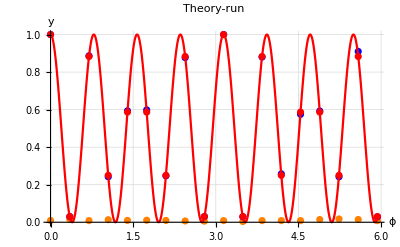

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

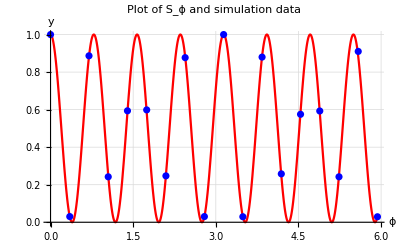

```mathematica
Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

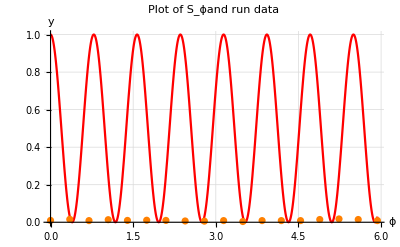

```mathematica
Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

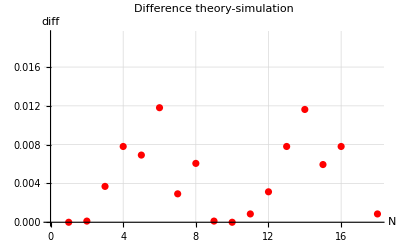

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

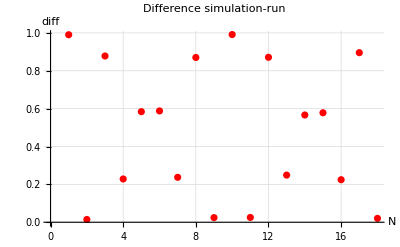

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

## N = 3 DISCUSS THEORY-SIMULATION-RUN

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=3;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

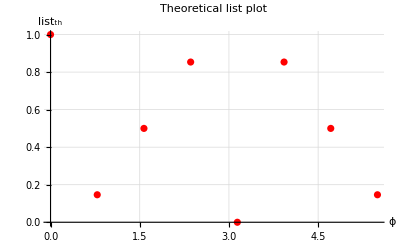

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

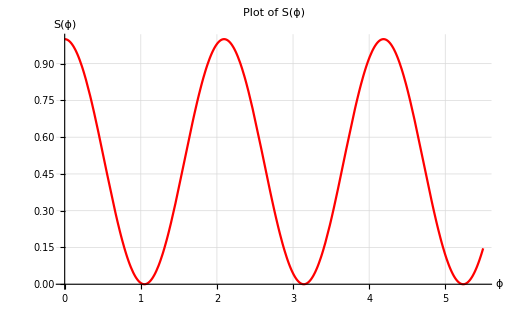

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

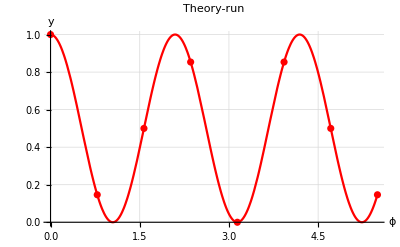

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

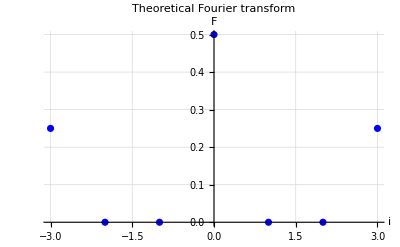

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

#### Data with the measurement of all qubit

```mathematica
data1={1.0,0.126953125,0.5087890625,0.8408203125,0.0,0.849609375,0.5234375,0.1591796875};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.126953,0.508789,0.84082,0.,0.849609,0.523438,0.15918}

8

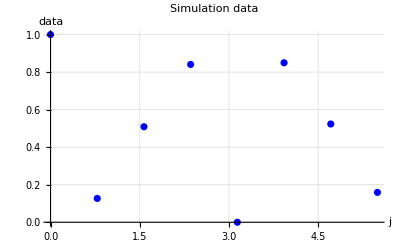

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

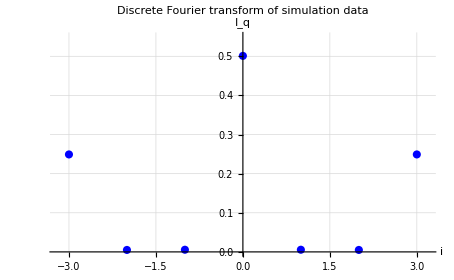

```mathematica
Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

#### Data with the measurement of all qubit (000)

```mathematica
data1={0.8115234375,0.2255859375,0.3759765625,0.7119140625,0.080078125,0.587890625,0.4228515625,0.1513671875}; (*Run on ibmqx2, 26 luglio 2019, ore 22:40*)
```

```mathematica
data2={}; (*Run on ibmqx4, 26 luglio 2019, ore *)
```

```mathematica
data3={0.7373046875,0.171875,0.5654296875,0.6123046875,0.146484375,0.708984375,0.3603515625,0.302734375}; (*Run on ibmq_16_melbourne, 25 luglio 2019, ore 23:38*)
```

#### Plot of the data choosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{0.811523,0.225586,0.375977,0.711914,0.0800781,0.587891,0.422852,0.151367}

8

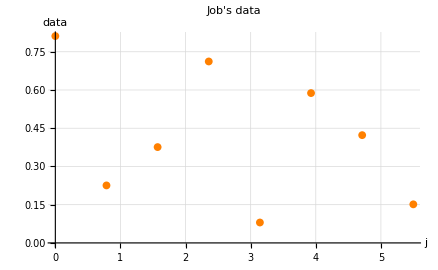

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

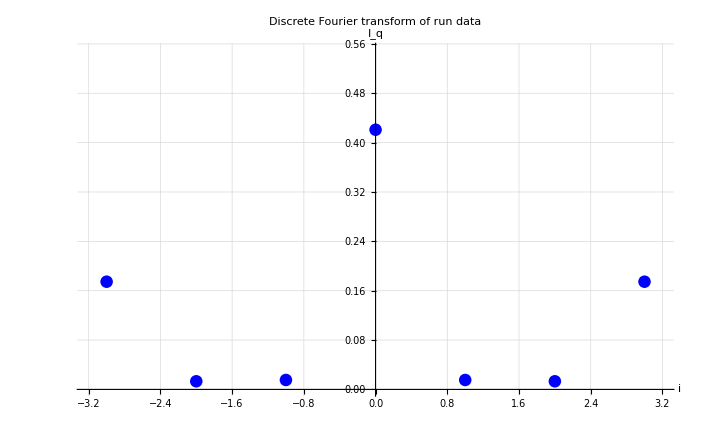

```mathematica
Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

COMPARE

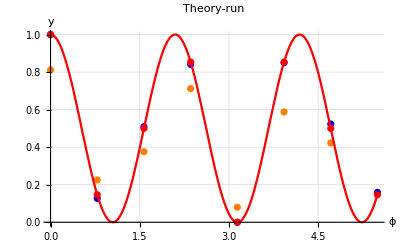

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

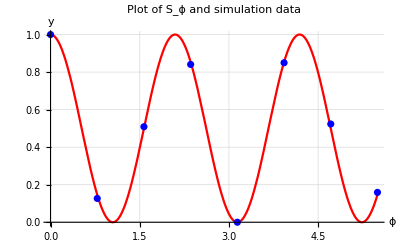

```mathematica
Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

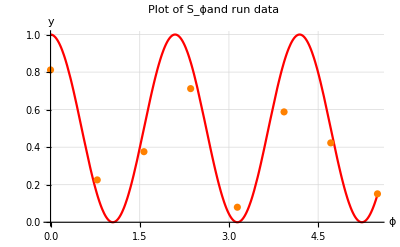

```mathematica
Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

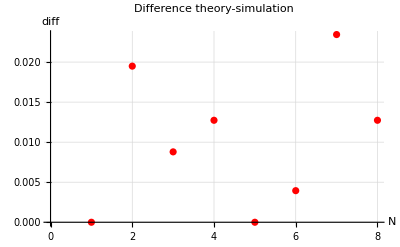

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

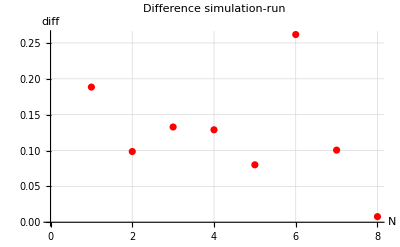

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

## N = 4 DISCUSS THEORY-SIMULATION-RUN

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=4;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

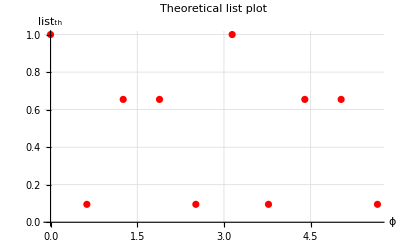

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

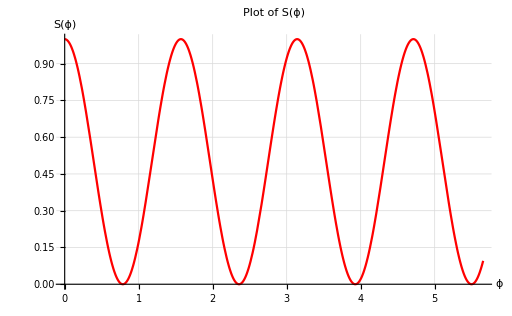

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

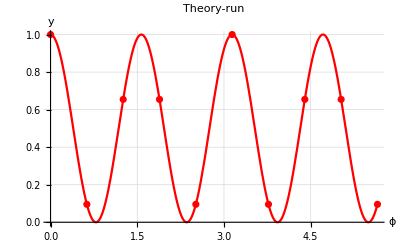

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

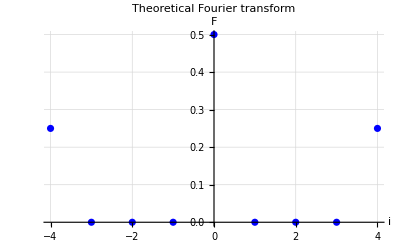

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

#### Data with the measurement of all qubit

```mathematica
data1={1.0,0.0888671875,0.662109375,0.662109375,0.0966796875,1.0,0.1025390625,0.6689453125,0.66015625,0.0947265625};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0888672,0.662109,0.662109,0.0966797,1.,0.102539,0.668945,0.660156,0.0947266}

10

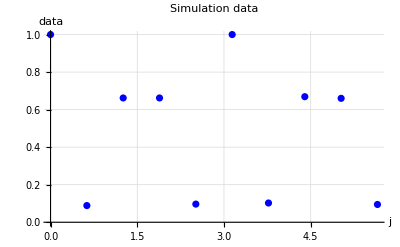

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

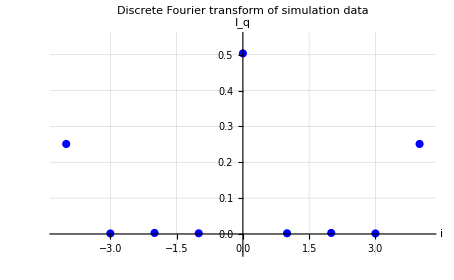

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.05,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

#### Data with the measurement of all qubit (000)

```mathematica
data1={0.4482421875,0.1259765625,0.2646484375,0.1689453125,0.2275390625,0.4912109375,0.154296875,0.2509765625,0.17578125,0.26171875}; (*Run on ibmqx2, 26 luglio 2019, ore 22:55*)
```

```mathematica
data2={0.4580078125,0.1396484375,0.2958984375,0.1474609375,0.2626953125,0.49609375,0.115234375,0.2822265625,0.16015625,0.2783203125}; (*Run on ibmqx2, 26 luglio 2019, ore 23:12*)
```

```mathematica
data3={}; (*Run on ibmq_16_melbourne, 25 luglio 2019, ore *)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.458008,0.139648,0.295898,0.147461,0.262695,0.496094,0.115234,0.282227,0.160156,0.27832}

10

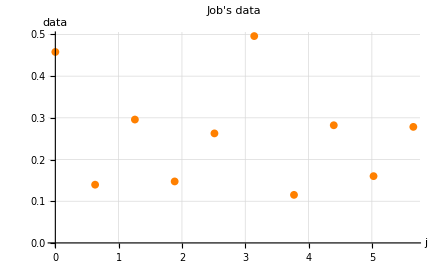

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

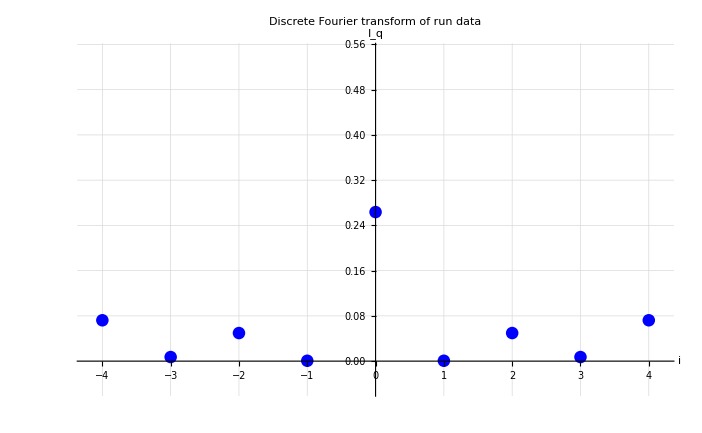

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{-0.05,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

COMPARE

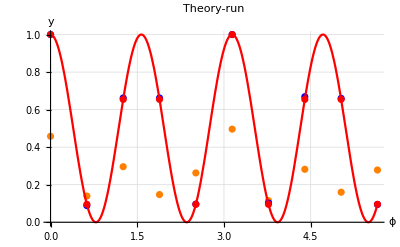

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

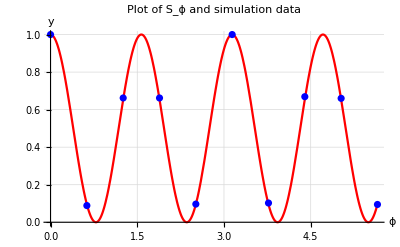

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

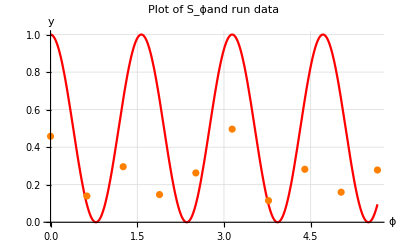

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

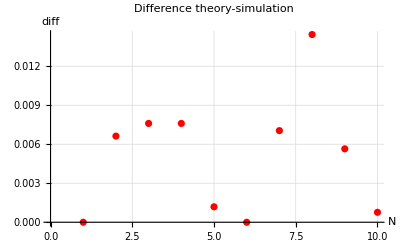

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

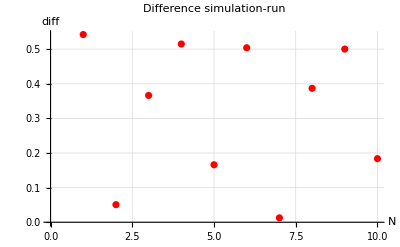

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

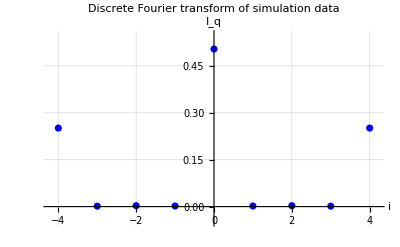

-Graphics-

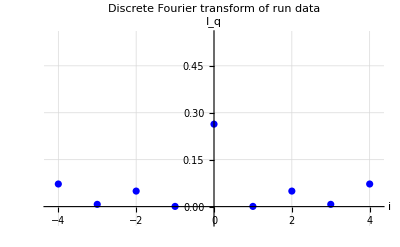

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```

## N = 5 DISCUSS THEORY-SIMULATION-RUN

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
```

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

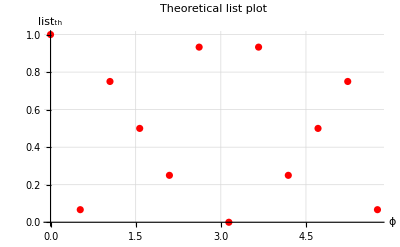

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

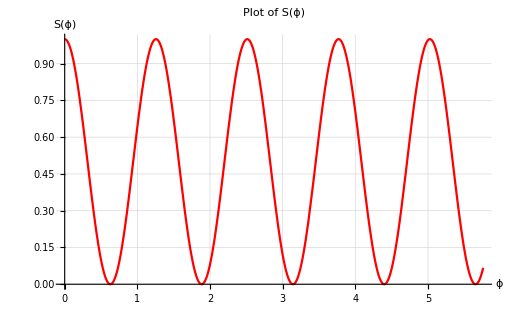

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

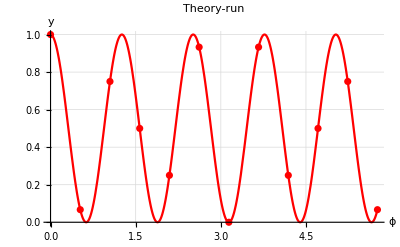

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

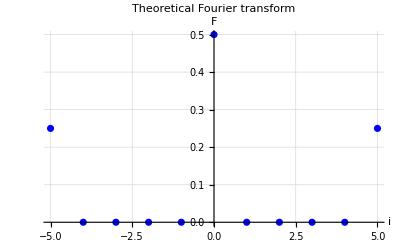

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

SIMULATION

#### Data with the measurement of all qubit

```mathematica
data1={1.0,0.0810546875,0.7470703125,0.5009765625,0.244140625,0.9267578125,0.0,0.9365234375,0.2470703125,0.5185546875,0.7373046875,0.0673828125};
```

#### Plot of the data choosen

```mathematica
simulation= data1
Length[simulation]
```

{1.,0.0810547,0.74707,0.500977,0.244141,0.926758,0.,0.936523,0.24707,0.518555,0.737305,0.0673828}

12

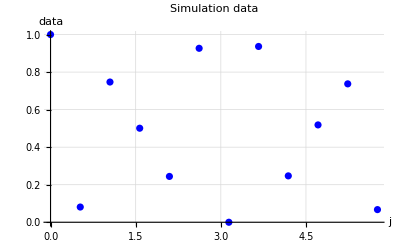

```mathematica
Subscript[plot, sim]=ListPlot[Thread[{Subscript[x, axis],simulation}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, sim]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*simulation[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

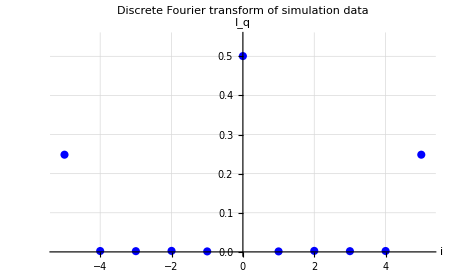

```mathematica
Subscript[I, sim]=Subscript[FPlot, sim]=ListPlot[Thread[{l,Subscript[F, sim]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

RUN

#### Data with the measurement of all qubit (000)

```mathematica
data1={0.275390625,0.220703125,0.3916015625,0.134765625,0.3828125,0.2431640625,0.21875,0.25390625,0.146484375,0.24609375,0.138671875,0.3662109375}; (*Run on ibmqx2, 27 luglio 2019, ore 9:07*)
```

```mathematica
data2={0.1474609375,0.1494140625,0.138671875,0.0869140625,0.08203125,0.083984375,0.119140625,0.1240234375,0.1162109375,0.103515625,0.09375,0.123046875}; (*Run on ibmq_16_melbourne, 27 luglio 2019, ore 12:58*)
```

#### Plot of the data choosen

```mathematica
run=data2  (*inserire il data che si vuole*)
Length[run]
```

{0.147461,0.149414,0.138672,0.0869141,0.0820313,0.0839844,0.119141,0.124023,0.116211,0.103516,0.09375,0.123047}

12

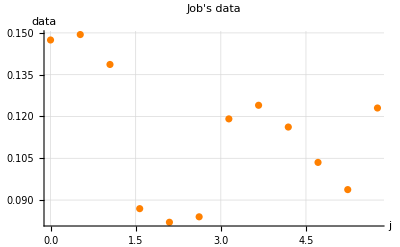

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

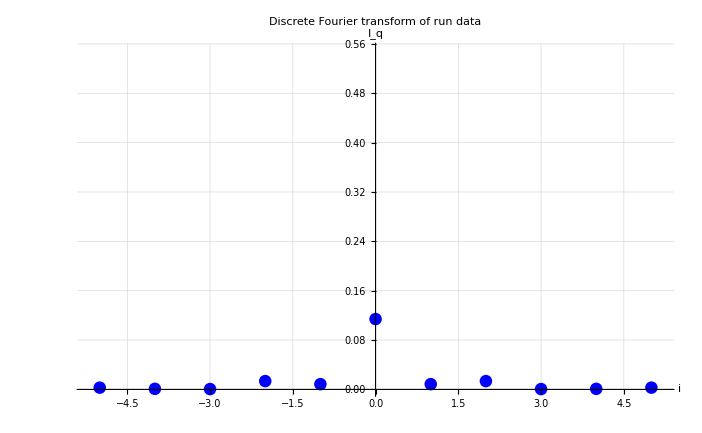

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

COMPARE

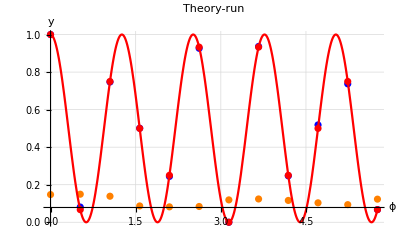

```mathematica
Show[Subscript[plot, run],Subscript[plot, sim],Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

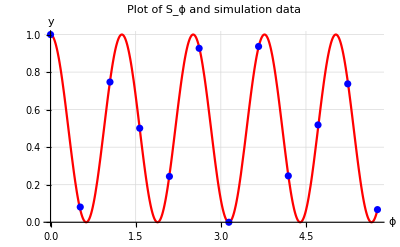

```mathematica
Subscript[S, sim]=Show[Subscript[plot, th],Subscript[plot, sim],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕ and simulation data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

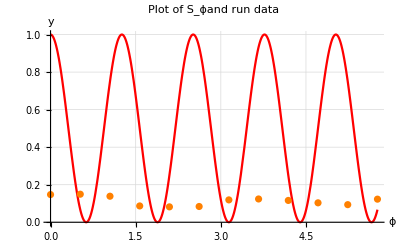

```mathematica
Subscript[S, run]=Show[Subscript[plot, th],Subscript[plot, run],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Plot of S_ϕand run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

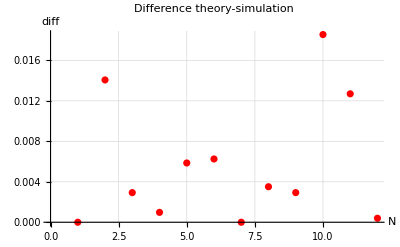

```mathematica
differenza=Abs[Subscript[list, th]-simulation];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference theory-simulation"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

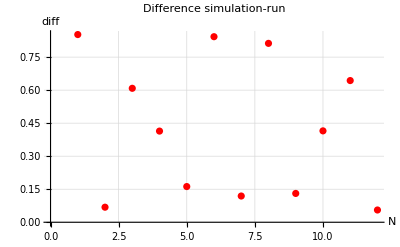

```mathematica
differenza=Abs[simulation-run];
ListPlot[differenza,AxesLabel->{HoldForm["N"],HoldForm["diff"]},PlotLabel->HoldForm["Difference simulation-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

Graphics to save

-Graphics-

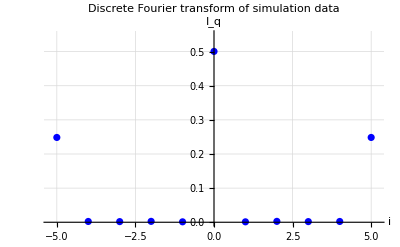

-Graphics-

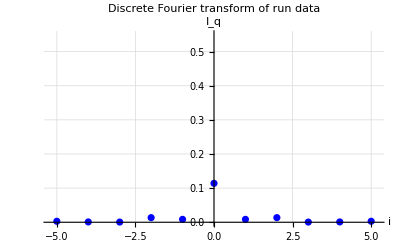

```mathematica
Subscript[S, sim]
Subscript[I, sim]
Subscript[S, run]
Subscript[I, run]
```